```mathematica
K = {{1-a-b,c,d},{a,1-c,0},{b,0,1-d}}
```

{{0.5,0.5,d},{0.5,0.5,0},{4.25×10^-9,0,1-d}}

```mathematica
MatrixForm[K]
```

(1-a-b | c | d
a | 1-c | 0
b | 0 | 1-d)

```mathematica
Simplify[Eigenvalues[K]]
```

{1,1/2 (2-a-b-c-d-√(a^2+2 a (b+c-d)+(b-c+d)^2)),1/2 (2-a-b-c-d+√(a^2+2 a (b+c-d)+(b-c+d)^2))}

```mathematica
Eigenvectors[K]
```

{{d/b,(a d)/(b c),1},{-(a+b+c-d+√(a^2+2 a b+b^2+2 a c-2 b c+c^2-2 a d+2 b d-2 c d+d^2))/(2 b),-(-a+b-c+d-√(a^2+2 a b+b^2+2 a c-2 b c+c^2-2 a d+2 b d-2 c d+d^2))/(2 b),1},{-(a+b+c-d-√(a^2+2 a b+b^2+2 a c-2 b c+c^2-2 a d+2 b d-2 c d+d^2))/(2 b),-(-a+b-c+d+√(a^2+2 a b+b^2+2 a c-2 b c+c^2-2 a d+2 b d-2 c d+d^2))/(2 b),1}}

```mathematica
RowReduce[K]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
X[t_]:={F[t],R[t],S[t]};
```

```mathematica
system = MapThread[#1==#2&,{X'[t],K.X[t]}]
```

{F'[t]==0.5 F[t]+0.5 R[t]+d S[t],R'[t]==0.5 F[t]+0.5 R[t],S'[t]==4.25×10^-9 F[t]+(1-d) S[t]}

```mathematica
sol = DSolve[system, {F,R,S}, t]
```

```mathematica
a = 0.5;
b = 4.25*^-9;
c = 0.5;
```

```mathematica
K
```

{{0.5,0.5,d},{0.5,0.5,0},{4.25×10^-9,0,1-d}}

```mathematica
testSol = ParametricNDSolve[{system, F[0]== 10, R[0]==0, S[0]==0},{F,R,S},{t,0,100},{d}]
```

{F→ParametricFunction[<>],R→ParametricFunction[<>],S→ParametricFunction[<>]}

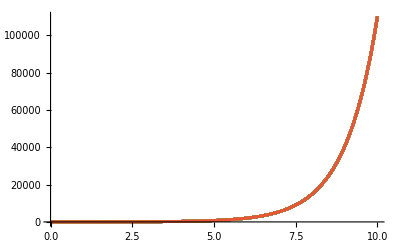

```mathematica
Plot[Evaluate[Table[F[d][t]/.testSol,{d,0,10,.1}]],{t,0,10},
 PlotRange->All]
```

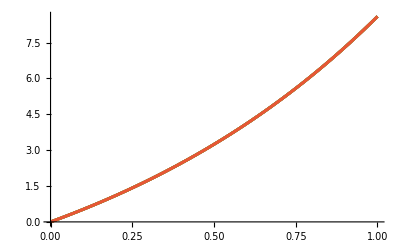

```mathematica
Plot[Evaluate[Table[R[d][t]/.testSol,{d,0,1,.1}]],{t,0,1},
 PlotRange->All]
```

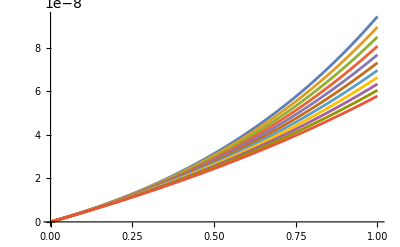

```mathematica
Plot[Evaluate[Table[S[d][t]/.testSol,{d,0,1,.1}]],{t,0,1},
 PlotRange->All]
```